# Лабораторная 7. Шаблоны и правила преобразований

Задание 1. Напишите шаблоны, означающие Log от любого аргумента; переменная x в целочисленной степени; сумма двух выражений; непустой список; произвольный список, включая пустой. Проверьте правильность с помощью команды MatchQ.

```mathematica
MatchQ[Log[2],Log[_]]
MatchQ[x^3,x^n_Integer] 
MatchQ[a+b,x_+y_]
MatchQ[{1,2,3},{__}]
MatchQ[{},{___}]
```

True

True

True

«2 more identical outputs»

```mathematica
Log[_]
x^n_Integer
x_+y_
MatchQ[Log[2],Log[_]]
MatchQ[{x,a},List[__]]
MatchQ[{},List[___]]
```

Задание 2. В тригонометрическом выражении, содержащем косинусы и синусы (например, Cos[x/3]^2+Sin[y]^2+Log[x]), замените все аргументы на половинные. Используйте команду ReplaceAll.

```mathematica
ClearAll[x,y,expr];
expr=Cos[x/3]^2+Sin[y]^2+Log[x];
ReplaceAll[expr,{Cos[arg_]->Cos[arg/2],Sin[arg_]->Sin[arg/2]}]
```

Cos[x/6]^2+Log[x]+Sin[y/2]^2

```mathematica
Cos[x/3]^2+Sin[y]^2+Log[x]/.{f_[x_]->f[x/2]}
Cos[x/3]^2+Sin[y]^2+Log[x]/.{Sin[x_]->Sin[x/2],Cos[x_]->Cos[x/2]}
```

Задание 3. Объясните результат работы команд:

Задание 4. Дан список z={1,2,0,3,4,s,g,j,k,4,2,1+I*7}. 
Посчитайте число ненулей в списке (Count, PatternTest или Except), 
количество комплексных чисел в списке; 
отберите элементы, являющиеся четными числами (Cases, PatternTest, EvenQ);
удалите четные числа из списка (DeleteCases, PatternTest, EvenQ); 
выпишите позиции чисел, больших 0 (Position, PatternTest). 
С помощью команд ReplaceRepeated и Condition напишите команду, вырезающую из данного списка первые 5 элементов; 
сравните с работой встроенной команды Drop.

```mathematica
ClearAll[z,s,g,j,k,x,y];
z={1,2,0,3,4,s,g,j,k,4,2,1+I*7};
Count[z,Except[0]]
Count[z,_Complex]
Cases[z,_?EvenQ]
DeleteCases[z,_?EvenQ]
Position[z,_?Positive] 
z//.{x___,y___}:>{y}/;Length[{x}]==5
Drop[z,5]
```

11

1

{2,0,4,4,2}

{1,3,s,g,j,k,1+7 ⅈ}

{{1},{2},{4},{5},{10},{11}}

{2,1+7 ⅈ}

{s,g,j,k,4,2,1+7 ⅈ}

Задание 5. Определите функцию, равную Cos при положительных значениях аргумента, и Cosh --- при отрицательных. Используйте команду: 1) Condition, 2) Piecewise. Постройте график. Распространите на эту функцию действие операции дифференцирования (TagSet).

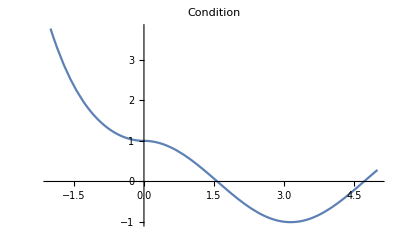

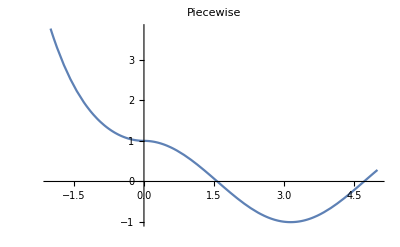

Piecewise[{{Sinh[x], x<0}, {0, x==0}, {-Sin[x], True}}]

Piecewise[{{-Sin[x], x>0}, {Sinh[x], x≤0}, {0, True}}]

```mathematica
ClearAll[f,g,x];
f[x_]:=Cos[x]/;x>0;
f[x_]:=Cosh[x]/;x≤0;
g[x_]:=Piecewise[{{Cos[x],x>0},{Cosh[x],x≤0}}];
Plot[f[x],{x,-2,5},PlotLabel->"Condition"]
Plot[g[x],{x,-2,5},PlotLabel->"Piecewise"]

f/:D[f[x_],x_]:=Piecewise[{{-Sin[x],x>0},{Sinh[x],x≤0}}];
D[g[x],x]
D[f[x],x]
```

```mathematica
Clear[f,g]
f[x_]:=Cos[x]/;x>0
f[x_]:=Cosh[x]/;x<=0
Plot[f[x],{x,-2,5}]
g[x_]=Piecewise[{{Cos[x],x>0},{Cosh[x],x<=0}}]
Plot[g[x],{x,-2,5}]
f/:D[f[x_],x_]:=Piecewise[{{-Sin[x],x>0},{Sinh[x],x<=0}}]
D[f[x],x]
```

Задание 6. Определите функцию, в которую можно подставлять любое ненулевое число аргументов и которая вычисляет среднее арифметическое с весами 1/k.

```mathematica
ClearAll[z,i];
weightedMean[z__]:=Module[{list={z},n},n=Length[list];
Sum[list[[i]]*(1/i),{i,1,n}]/Sum[1/i,{i,1,n}]];

weightedMean[]
weightedMean[1,2,3]
```

weightedMean[]

18/11

```mathematica
meanw[z0__]:=Module[{s,z},Print[z0];z=List[z0] ;Print[z];s=Sum[z[[i]]/i,{i,Length[z]}]/Sum[1/i,{i,Length[z]}]]
meanw[a,b,c]
```

Задание 7. Смоделируйте команду Apply замены заголовка выражения на данный с помощью шаблона.

```mathematica
ClearAll[myApply,newHead,head,args,a,b,c];
myApply[newHead_,head_[args___]]:=newHead[args];

myApply[Times,a+b+c]
myApply[List,f[1,2,3]]
```

a b c

{1,2,3}

```mathematica
apply[g_,f_[z___]]:=g[z]
apply[Cos,Sin[x]]
Clear[a,b,c]
apply[List,a+b+c]
apply[Times,a+b+c]
```

Задание 8. Для данного n сформируйте список z, состоящий из n различных чисел. Дана функция f. Разделенные разности функции f образуют таблицу. В первой строке стоят значения функции f_i^[0]=f(z_i). Вторая строка состоит из чисел f_i^[1]=(f_(i+1)^[0]-f_i^[0])/(z_(i+1)-z_i). Следующая строка строится по второй по тому же правилу: f_i^[2]=(f_(i+1)^[1]-f_i^[1])/(z_(i+2)-z_i). И т.д. Постройте таблицу из разделенных разностей. Оформите результат в виде Module. Как проверить правильность работы?

```mathematica
ClearAll[f,z,n];
divDiffTable[f_,z_List]:=Module[{n=Length[z],dd},dd[i_,i_]:=f[z[[i]]];
dd[i_,j_]:=dd[i,j]=(dd[i+1,j]-dd[i,j-1])/(z[[j]]-z[[i]]);
TableForm[Table[dd[j,j+i],{i,0,n-1},{j,1,n-i}]]];

f[x_]:=x^2+2 x+1;
z={1,2,4,7,11};
divDiffTable[f,z]
```

4 | 9 | 25 | 64 | 144
5 | 8 | 13 | 20 | 
1 | 1 | 1 |  | 
0 | 0 |  |  | 
0 |  |  |  |

Задание 9.  Двумерное нормальное распределение задается плотностью вероятности f[x_,y_]:=1/(2*Pi*sigma1*sigma2*Sqrt[1-cor^2])*Exp[-1/(2*(1-cor^2))*((x-a1)^2/sigma1^2+(y-a2)^2/sigma2^2-2*cor*((x-a1)*(y-a2))/(sigma1*sigma2))]. А двумерное полиномиальное распределение имеет распределение вероятности  pr[k_,l_,m_]=Multinomial[k,l,m] p^k q^l r^m, где r:=1-p-q, m:=n-k-l. Постройте графики этих функций (команды Plot3D и ListPointPlot3D). Для p=1/2, q=1/3 и n=50 подберите параметры нормального распределения так, чтобы f приближала pr (двумерный аналог локальной теоремы Муавра--Лапласа). Указание. Рассмотрите зависимость pr только от k и l. Вначале покажите, что математическим ожиданием полиномиального распределения является (np,nq). Затем вычислите выборочные дисперсии и коэффициент корреляции и возьмите их в качестве sigma1, sigma2 и cor.

```mathematica
ClearAll[f,pr,p,q,r,n,k,l,m,a1,a2,varK,varL,covKL,sigma1,sigma2,cor,pts,plot1,plot2];

p=1/2;q=1/3;n=50;
r:=1-p-q;
m:=n-k-l;

pr[k_,l_]:=Multinomial[k,l,m]*p^k*q^l*r^m;

f[x_,y_]:=1/(2*Pi*sigma1*sigma2*Sqrt[1-cor^2])*Exp[-1/(2*(1-cor^2))*((x-a1)^2/sigma1^2+(y-a2)^2/sigma2^2-2*cor*((x-a1)*(y-a2))/(sigma1*sigma2))]


pts=Flatten[Table[{k,l,N[pr[k,l]]},{k,0,n},{l,0,n-k}],1];

a1=n*p;
a2=n*q;

meanCheckK=Sum[(k-a1)*N[pr[k,l]],{k,0,n},{l,0,n-k}]
meanCheckL=Sum[(l-a2)*N[pr[k,l]],{k,0,n},{l,0,n-k}]

varK=Sum[(k-a1)^2*N[pr[k,l]],{k,0,n},{l,0,n-k}];
varL=Sum[(l-a2)^2*N[pr[k,l]],{k,0,n},{l,0,n-k}];
covKL=Sum[(k-a1)*(l-a2)*N[pr[k,l]],{k,0,n},{l,0,n-k}];

sigma1=Sqrt[varK];
sigma2=Sqrt[varL];
cor=covKL/(sigma1*sigma2);

plot1=ListPointPlot3D[pts,PlotStyle->Red,PlotRange->All];
plot2=Plot3D[f[x,y],{x,0,n},{y,0,n},PlotRange->All,PlotStyle->Opacity[0.6]];

Show[plot1,plot2]
```

-3.40931×10^-20

1.08786×10^-16

-Graphics3D-

```mathematica
f[x_,y_]:=1/(2*Pi*sigma1*sigma2*Sqrt[1-cor^2])*Exp[-1/(2*(1-cor^2))*((x-a1)^2/sigma1^2+(y-a2)^2/sigma2^2-2*cor*((x-a1)*(y-a2))/(sigma1*sigma2))]
(*"Проверка:" Integrate[f[x,y],{x,-Infinity,Infinity},{y,-Infinity,Infinity},Assumptions->0<cor<1]*)
r:=1-p-q;
m:=n-k-l;
pr[k_,l_,m_]:=Multinomial[k,l,m] p^k q^l r^m;
(*n=5
meanK=Sum[(k-n*p)*pr[k,l,m]//N,{k,0,n},{l,0,n-k}]//Simplify
meanL=Sum[(l-n*q)*pr[k,l,m]//N,{k,0,n},{l,0,n-k}]//Simplify*)

p=1/2;q=1/3;
n=50;
tab=Table[{k,l,pr[k,l,m]//N},{k,0,n},{l,0,n-k}];
fig1=ListPointPlot3D[tab,PlotRange->All];
meanK=Sum[(k-n*p)*pr[k,l,m]//N,{k,0,n},{l,0,n-k}];(*Проверка*)
meanL=Sum[(l-n*q)*pr[k,l,m]//N,{k,0,n},{l,0,n-k}];(*Проверка*)

a1=n*p;a2=n*q;
varKK=Sum[(k-n*p)^2*pr[k,l,m]//N,{k,0,n},{l,0,n-k}];
varLL=Sum[(l-n*q)^2*pr[k,l,m]//N,{k,0,n},{l,0,n-k}];
varKL=Sum[(k-n*p)*(l-n*q)*pr[k,l,m]//N,{k,0,n},{l,0,n-k}];
sigma1=Sqrt[varKK];sigma2=Sqrt[varLL];
cor=varKL/(sigma1*sigma2);

fig2=Plot3D[f[x,y],{x,0,n},{y,0,n},PlotRange->All,PlotPoints->50];
Show[fig1,fig2]
```

Задание 10. Напишите команду, вычисляющую градиент заданной функции n
переменных (используйте Apply или Outer}). Ср. с работой встроенной команды Grad.
Затем напишите команду, вычисляющую по заданной функции n переменных
и заданному n-мерному вектору производную этой функции в направлении этого
вектора.

```mathematica
ClearAll[myGrad,dirDeriv,f,x,y,z,vec];
myGrad[f_,n_]:=Module[{vars=Table[Subscript[x,i],{i,n}]},Map[D[Apply[f,vars],#]&,vars]];
dirDeriv[f_,vec_List]:=myGrad[f,Length[vec]].vec;
f[x_,y_,z_]:=x^2+y^3+x*z;
vec={1,2,-1};
myGrad[f,3]
Grad[f[Subscript[x,1],Subscript[x,2],Subscript[x,3]],{Subscript[x,1],Subscript[x,2],Subscript[x,3]}]
dirDeriv[f,vec]
```

{2 x_1+x_3,3 x_2^2,x_1}

{2 x_1+x_3,3 x_2^2,x_1}

x_1+6 x_2^2+x_3

```mathematica
f[x_,y_,z_]=x^2+y^2+z^4
grad[f_,n_]:=Map[D[f[Apply[Sequence,Table[Subscript[x,i],{i,n}]]],#]&,Table[Subscript[x,i],{i,n}]]
grad[f,3]
(*Нахождение производной по направлению:*)
vec={1,2,3}
f[x_,y_,z_]=x^2+y^2+z^4
vec.grad[f,3]
```

Задание 11. Создайте графики суперпозиций всех тригонометрических функций
и обратных к ним в том и другом порядке. Используйте Thread и Composition.
Почему графики не совпадают с графиком  функции y=x?

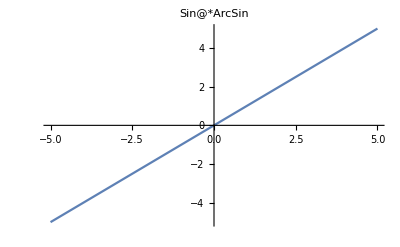
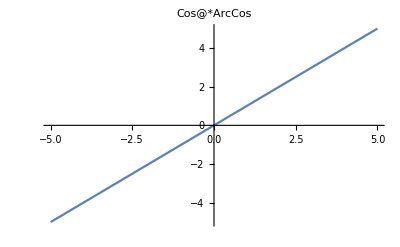
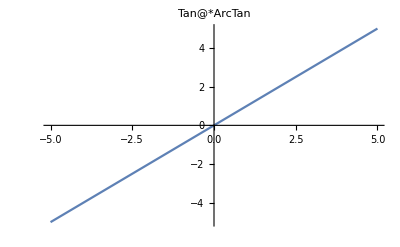
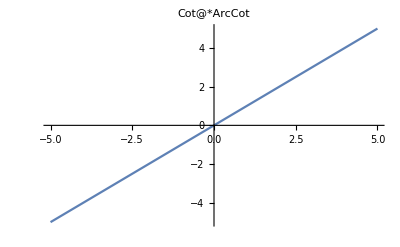

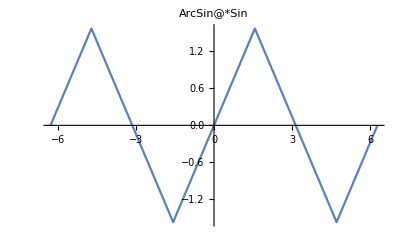
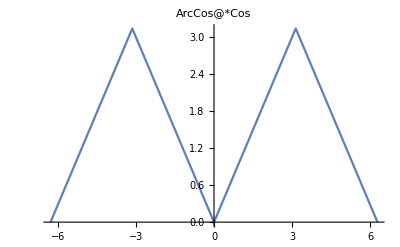
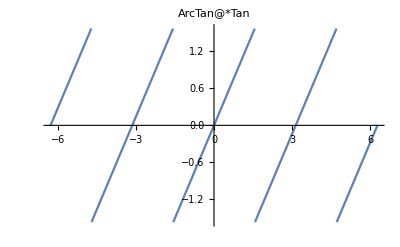
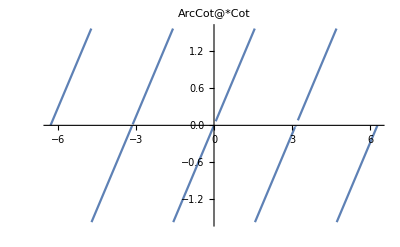

```mathematica
ClearAll[trig,invTrig,comp1,comp2,x];

trig={Sin,Cos,Tan,Cot};
invTrig={ArcSin,ArcCos,ArcTan,ArcCot};

comp1=Thread[Composition[trig,invTrig]];
Map[Plot[#[x],{x,-5,5},PlotLabel->#]&,comp1]

comp2=Thread[Composition[invTrig,trig]];
Map[Plot[#[x],{x,-2 Pi,2 Pi},PlotLabel->#]&,comp2]
```

```mathematica
direct={Cos,Sin,Tan,Cot}
inverse={ArcCos,ArcSin,ArcTan,ArcCot}
Map[Plot[#[x],{x,-10 Pi,10 Pi}]&,Thread[Composition[direct,inverse]]]
Map[Plot[#[x],{x,-10 Pi,10 Pi}]&,Thread[Composition[inverse,direct]]]
```

Задание 12. Напишите команду, преобразующую список {a,a,a,b,b,c,d,d,d,d,d} в {{a,3},{b,2},{c,1},{d,5}}. Желательно использовать командуReplaceRepeated (краткая форма --- //.).

```mathematica
ClearAll[rleEncode,lst,a,b,c,d,x,y,el,k,j];
lst={a,a,a,b,b,c,d,d,d,d,d};
rleEncode[list_List]:=Module[{pairs},pairs=Map[{#,1}&,list];
pairs//.{x___,{el_,k_},{el_,j_},y___}:>{x,{el,k+j},y}];
rleEncode[lst]
```

{{a,3},{b,2},{c,1},{d,5}}

```mathematica
uncode[l_List]:=Module[{l1},
l1=Map[{#,1}&,l];
l1//.{x___,{a_,k_},{a_,j_},y___} :> {x,{a,k+j},y}]
(*Проверка:*)
m={a,a,a,b,b,c,d,d,d,d,d}
uncode[m]
```